```mathematica
Clear[Dd,Ds]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!

Dd[n_,0,a_]:=UnitStep[n-1]
Dd[n_,1,a_]:=Dd[n,1,a]=Floor[n]-a
Dd[n_,2,a_]:=Dd[n,2,a]=Sum[ 1+2 (Dd[Floor[n/m],1,m]),{m,a+1,Floor[n^(1/2)]}]
Dd[n_,k_,a_]:=Dd[n,k,a]=Sum[1 +k Dd[Floor[n/(m^(k-1))],1, m]+Sum[bin[k,j]  Dd[Floor[n/(m^j)],k-j, m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]
Ddz[n_,  z_] := Expand[Sum[bin[z,k]Dd[n,k,1],{k,0,Log[2,n]}]]
Ddzeros[n_]:=List@@NRoots[Ddz[n,z]==0,z][[All,2]]
DdzAlt[n_, z_] := Expand[Product[ 1-z/rho,{rho,Ddzeros[n]}]]

Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[ (m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k)) +k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s, m]+Sum[bin[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s, m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]
Dsz[n_, s_, z_] := Expand[Sum[bin[z,k]Ds[n,k,s,1],{k,0,Log[2,n]}]]
Dszeros[n_,s_]:=List@@NRoots[Dsz[n,s,z]==0,z][[All,2]]
DszAlt[n_, s_,z_] := Expand[Product[ 1-z/rho,{rho,Dszeros[n,s]}]]

Ddy[n_,s_,y_,k_]:=y^(k(s-1)) Ds[n y^k,k,s,y]
Dyz[n_, s_, y_,z_] := Expand[Sum[bin[z,k]Ddy[n,s,y,k],{k,0,Log[(y+1)/y,n]}]]
Dyzeros[n_,s_,y_]:=List@@NRoots[Dyz[n,s,y,z]==0,z][[All,2]]
DyzAlt[n_, s_,y_, z_] := Expand[Product[ 1-z/rho,{rho,Dyzeros[n,s,y]}]]

Eabz[n_, s_,a_,b_,z_] := Expand[Sum[(-1)^j bin[z,j] (a/b)^(j(1-s))Dsz[ n/((a/b)^j),s,z],{j,0,Log[a/b,n]}]]
Eabzeros[n_,s_,a_, b_]:=List@@Roots[Eabz[n,s,a,b,z]==0,z][[All,2]]

Ez[n_, s_,z_] := Expand[Sum[ (-1)^j bin[z,j] 2^(j(1-s))Dsz[ n/(2^j),s,z],{j,0,Log[2,n]}]]
Ezeros[n_,s_,y_]:=List@@NRoots[Ez[n,s,y,z]==0,z][[All,2]]
```

```mathematica
N[Ddy[100,N[ZetaZero[1]],10,2]]
```

2.34019-2.15473 ⅈ

```mathematica
tt[n_, s_] := 1/(s-1)^2 Gamma[ 2,0,(s-1)Log[n]]/Gamma[2]
```

```mathematica
N[tt[100,N[ZetaZero[1]]]]
```

2.39654-2.19631 ⅈ

```mathematica
Eabz[100,0,1,101,1,z]//TableForm
```

0 | 1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Floor[Log[4/3,100.]]
```

16

```mathematica
Floor[Log[3/2,100.]]
```

11

```mathematica
Floor[Log[4/3,100.]]
```

16

```mathematica
Floor[Log[5/4,100.]]
```

20

```mathematica
Dyzeros[20,0,18]
```

{-16617.9-5237.57 ⅈ,-16617.9+5237.57 ⅈ,-9290.99-11911. ⅈ,-9290.99+11911. ⅈ,-3934.78-3646.03 ⅈ,-3934.78+3646.03 ⅈ,-1482.99-336.133 ⅈ,-1482.99+336.133 ⅈ,-1211.85-949.506 ⅈ,-1211.85+949.506 ⅈ,-550.272,-527.403-11813.1 ⅈ,-527.403+11813.1 ⅈ,-507.145-1621.42 ⅈ,-507.145+1621.42 ⅈ,-370.357,-211.949-160.191 ⅈ,-211.949+160.191 ⅈ,-120.769,-120.697-538.177 ⅈ,-120.697+538.177 ⅈ,-89.3935-1159.2 ⅈ,-89.3935+1159.2 ⅈ,-73.4803-203.301 ⅈ,-73.4803+203.301 ⅈ,-61.6191,-51.4836-86.044 ⅈ,-51.4836+86.044 ⅈ,-20.9516-23.3877 ⅈ,-20.9516+23.3877 ⅈ,-19.6897-46.7512 ⅈ,-19.6897+46.7512 ⅈ,-16.2911-86.5774 ⅈ,-16.2911+86.5774 ⅈ,-16.035-12.1799 ⅈ,-16.035+12.1799 ⅈ,-15.5,-7.09099-1.61247 ⅈ,-7.09099+1.61247 ⅈ,-2.16918,-0.136789,10.3212-146.17 ⅈ,10.3212+146.17 ⅈ,72.5801-229.225 ⅈ,72.5801+229.225 ⅈ,199.522-347.037 ⅈ,199.522+347.037 ⅈ,476.359-557.924 ⅈ,476.359+557.924 ⅈ,726.459-1823.6 ⅈ,726.459+1823.6 ⅈ,1300.57-1174.34 ⅈ,1300.57+1174.34 ⅈ,5492.2-5648.27 ⅈ,5492.2+5648.27 ⅈ}

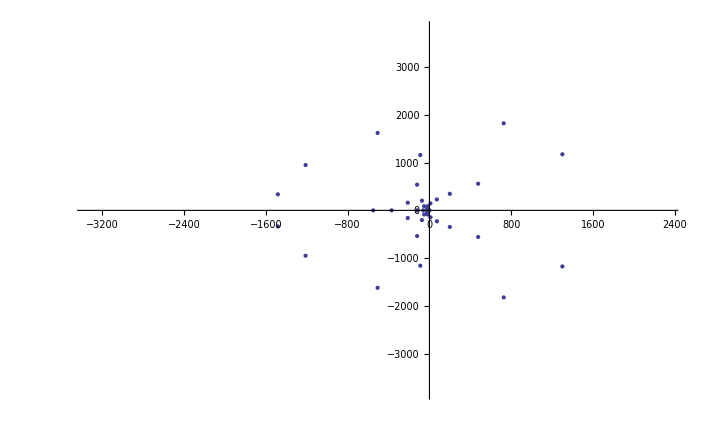

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,Dyzeros[20,0,18]}]]
```

```mathematica
AbsoluteTiming[Dz[10000000,z]]
```

{3.448197,1+(3559637526370229 z)/5354228880+(1989544871269240547 z^2)/921858537600+(2021824016451264335171 z^3)/677566025136000+(7019677821920298561119 z^4)/2956651746048000+(6419737164240558941381 z^5)/5217620728320000+(355971199127948600783 z^6)/800296713216000+(87671088330394680791 z^7)/750278168640000+(647852562694427393 z^8)/28245766348800+(1156246192125011873 z^9)/337983528960000+(6208422327896021939 z^10)/15817629155328000+(250225399924000051 z^11)/7189831434240000+(6106970322634813 z^12)/2549361475584000+(63437608022863169 z^13)/497125487738880000+(47189432328823 z^14)/9038645231616000+(17111105280953 z^15)/105450861035520000+(120162307939 z^16)/31635258310656000+(179878582253 z^17)/2688996956405760000+(2349779 z^18)/2845499424768000+(53393233 z^19)/7298706024529920000+(94223 z^20)/2919482409811968000+(13 z^21)/154120489205760000+(53 z^22)/224800145555521536000+z^23/25852016738884976640000}

```mathematica
AbsoluteTiming[Dsz[10000000,0,z]]
```

{5.297303,1+(3559637526370229 z)/5354228880+(1989544871269240547 z^2)/921858537600+(2021824016451264335171 z^3)/677566025136000+(7019677821920298561119 z^4)/2956651746048000+(6419737164240558941381 z^5)/5217620728320000+(355971199127948600783 z^6)/800296713216000+(87671088330394680791 z^7)/750278168640000+(647852562694427393 z^8)/28245766348800+(1156246192125011873 z^9)/337983528960000+(6208422327896021939 z^10)/15817629155328000+(250225399924000051 z^11)/7189831434240000+(6106970322634813 z^12)/2549361475584000+(63437608022863169 z^13)/497125487738880000+(47189432328823 z^14)/9038645231616000+(17111105280953 z^15)/105450861035520000+(120162307939 z^16)/31635258310656000+(179878582253 z^17)/2688996956405760000+(2349779 z^18)/2845499424768000+(53393233 z^19)/7298706024529920000+(94223 z^20)/2919482409811968000+(13 z^21)/154120489205760000+(53 z^22)/224800145555521536000+z^23/25852016738884976640000}

```mathematica
Chop[Expand[DdAlt[100,z]]]
```

1+28.5333 z+45.2472 z^2+20.6875 z^3+4.24306 z^4+0.279167 z^5+0.00972222 z^6

```mathematica
Chop[Expand[Product[1 -z/j,{j,Dszeros[100,0]}]]]
```

1+28.5333 z+45.2472 z^2+20.6875 z^3+4.24306 z^4+0.279167 z^5+0.00972222 z^6

```mathematica
Chop[Expand[Product[1 -z/j,{j,Dyzeros[100,0,10]}]]]
```

1+28.1899 z+40.6568 z^2+22.3167 z^3+6.51591 z^4+1.16695 z^5+0.140813 z^6+0.0121152 z^7+0.000776657 z^8+0.0000383027 z^9+1.48643×10^-6 z^10+4.64176×10^-8 z^11+1.18316×10^-9 z^12

```mathematica
N[Eabz[100, -1,20,19,z]]
```

1.-60.5515 z+39.6222 z^2+274.169 z^3-767.594 z^4+1030.97 z^5-981.742 z^6+774.004 z^7-484.117 z^8+249.592 z^9-107.668 z^10+39.2515 z^11-12.2222 z^12+3.28829 z^13-0.77276 z^14+0.160122 z^15-0.0294805 z^16+0.00485235 z^17-0.000717251 z^18+0.0000954802 z^19-0.0000114556 z^20+1.23646×10^-6 z^21-1.19357×10^-7 z^22+1.01712×10^-8 z^23-7.43486×10^-10 z^24+4.32745×10^-11 z^25-1.47541×10^-12 z^26-6.67×10^-14 z^27+1.92003×10^-14 z^28-2.36181×10^-15 z^29+2.2285×10^-16 z^30-1.79429×10^-17 z^31+1.28291×10^-18 z^32-8.30777×10^-20 z^33+4.92861×10^-21 z^34-2.69861×10^-22 z^35+1.37086×10^-23 z^36-6.48586×10^-25 z^37+2.86666×10^-26 z^38-1.18652×10^-27 z^39+4.6083×10^-29 z^40-1.68233×10^-30 z^41+5.78112×10^-32 z^42-1.87234×10^-33 z^43+5.72132×10^-35 z^44-1.651×10^-36 z^45+4.50283×10^-38 z^46-1.16146×10^-39 z^47+2.83496×10^-41 z^48-6.55122×10^-43 z^49+1.4338×10^-44 z^50-2.97282×10^-46 z^51+5.84041×10^-48 z^52-1.08732×10^-49 z^53+1.91829×10^-51 z^54-3.20687×10^-53 z^55+5.07912×10^-55 z^56-7.61942×10^-57 z^57+1.08226×10^-58 z^58-1.45487×10^-60 z^59+1.84997×10^-62 z^60-2.22368×10^-64 z^61+2.52475×10^-66 z^62-2.70538×10^-68 z^63+2.7332×10^-70 z^64-2.60053×10^-72 z^65+2.32732×10^-74 z^66-1.95631×10^-76 z^67+1.54214×10^-78 z^68-1.138×10^-80 z^69+7.8457×10^-83 z^70-5.04228×10^-85 z^71+3.01326×10^-87 z^72-1.66968×10^-89 z^73+8.55099×10^-92 z^74-4.03269×10^-94 z^75+1.74396×10^-96 z^76-6.88211×10^-99 z^77+2.46415×10^-101 z^78-7.95143×10^-104 z^79+2.29373×10^-106 z^80-5.85714×10^-109 z^81+1.30788×10^-111 z^82-2.51441×10^-114 z^83+4.07773×10^-117 z^84-5.42456×10^-120 z^85+5.68363×10^-123 z^86-4.39796×10^-126 z^87+2.23442×10^-129 z^88-5.5912×10^-133 z^89

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,Eabzeros[100,0,35,34]}]]
```

$Aborted

```mathematica
Ddzeros[100000000]
```

{-7494.07,-1440.44,-281.526,-37.2362-148.713 ⅈ,-37.2362+148.713 ⅈ,-35.5639,-13.9034-54.5839 ⅈ,-13.9034+54.5839 ⅈ,-13.5241-33.6412 ⅈ,-13.5241+33.6412 ⅈ,-11.5772-12.0093 ⅈ,-11.5772+12.0093 ⅈ,-6.16326-16.2264 ⅈ,-6.16326+16.2264 ⅈ,-4.59605-8.12566 ⅈ,-4.59605+8.12566 ⅈ,-4.13439-4.72012 ⅈ,-4.13439+4.72012 ⅈ,-3.44066-2.91838 ⅈ,-3.44066+2.91838 ⅈ,-2.68701-1.52872 ⅈ,-2.68701+1.52872 ⅈ,-1.94007-0.419915 ⅈ,-1.94007+0.419915 ⅈ,-0.99477,-1.73548×10^-7}

```mathematica
Ddz[100000000,z]
```

1+(6427431691337929 z)/1115464350+(2516314672020796036867 z^2)/128629994613120+(3575746713648621345062531 z^3)/124672148625024000+(20380394053499739865496567 z^4)/831147657500160000+(1351629191016384695492785649 z^5)/97569507619584000000+(240272276318313590611783219 z^6)/43364225608704000000+(41833655627451907360857929 z^7)/25545471085854720000+(3761102376291956378646751 z^8)/10218188434341888000+(5175675474335907053437241 z^9)/80669908692172800000+(1418826547912276016443177 z^10)/161339817384345600000+(279266312199608569103 z^11)/292017769021440000+(1386818791325659005283 z^12)/16703416388026368000+(4814640871442135348159 z^13)/835170819401318400000+(3482068013538497942357 z^14)/10857220652217139200000+(1188915869941720073 z^15)/83517081940131840000+(4192807585604237 z^16)/8351708194013184000+(17963977627832867 z^17)/1290718539074764800000+(390742194213977 z^18)/1290718539074764800000+(1555110247813 z^19)/306545653030256640000+(31437955243 z^20)/490473044848410624000+(14797988921 z^21)/24523652242420531200000+(976022221 z^22)/269760174666625843200000+(786869 z^23)/47726800133326110720000+(1493 z^24)/38778025108327464960000+(727 z^25)/31022420086661971968000000+z^26/403291461126605635584000000

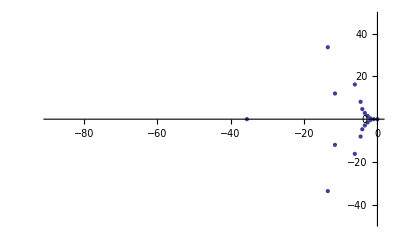

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,Ddzeros[100000000]}]]
```